# Stochastic Differential Equations with Mathematica

## About the author

Author : Nelson Mok
email : madeinquant@gmail.com

### Summary

The Mathematica versions in Higham “An Algorithmic Introduction to Numerical Simulation of Stochastic Differential Equations”, SIAM Review, Vol. 43, No. 3, 2001.

The Details can be found in the paper (http://www.caam.rice.edu/~cox/stoch/dhigham.pdf)

## standard Wiener process, looping & vector ( bpath1.m & bpath2.m)

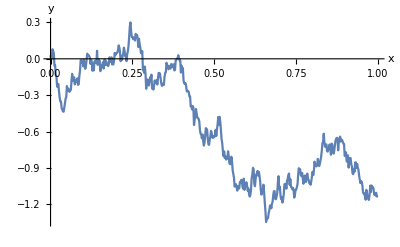
-Graphics-tW(t)

```mathematica
start = 0.0;
T = 1.0;
steps = 500;
dt = T / steps;
t = Range[start,T-dt,dt];
W = Table[0.0,steps];
dW = Table[0.0,steps];

(* 
dW[[1]] = RandomReal[NormalDistribution[0,1]];
W[[1]] = dW[[1]];

For[j=2,j<steps+1,j++,
dW[[j]] = Sqrt[dt] * RandomReal[NormalDistribution[0,1]];
W[[j]] = W[[j-1]] + dW[[j]]
];
*)

dW = Sqrt[dt] * RandomReal[NormalDistribution[0,1],steps];
W = Accumulate[dW];

ts = TimeSeries[W,{t}];
(* ListLinePlot[ts]*)

Labeled[ListLinePlot[ts,AxesLabel->{"x","y"}],{"t","W(t)"},{Bottom,Left},RotateLabel->True]
```

## bpath3

{0.974804,0.970667,0.94239,0.94416,0.963171,0.96648,0.962379,0.973697,0.977407,0.96685,0.98963,0.977125,1.03129,0.996826,0.991023,0.962625,0.928541,0.944739,0.943687,0.957742,0.953635,0.957949,0.97959,0.974183,1.00528,1.01728,1.02588,1.05398,1.11877,1.16768,1.19737,1.23263,1.21308,1.24091,1.23558,1.20035,1.24023,1.25037,1.27324,1.29386,1.30403,1.29809,1.3355,1.35475,1.3246,1.34159,1.37599,1.3331,1.37712,1.4423,1.44305,1.44886,1.45314,1.41293,1.44858,1.43738,1.47219,1.48404,1.48391,1.51263,1.50529,1.56404,1.52558,1.49301,1.5027,1.54811,1.56758,1.62958,1.70632,1.76746,1.77654,1.77251,1.77176,1.79265,1.77821,1.7907,1.81165,1.89801,1.86088,1.79864,1.74483,1.70697,1.78784,1.77393,1.75329,1.77501,1.81548,1.82218,1.82921,1.77831,1.76073,1.81779,1.85973,1.77224,1.7731,1.80075,1.78586,1.74398,1.78151,1.8581,1.91291,1.81831,1.83287,1.84753,1.92471,1.9456,1.99592,1.99279,1.9406,1.94622,1.95174,1.89557,1.85598,1.90623,1.8968,1.91798,1.93594,1.95393,1.9872,1.89378,1.90308,1.88399,1.92139,1.91714,1.9698,1.98929,1.89196,1.97847,2.03222,2.07077,2.05006,2.1193,2.11314,2.0595,2.17482,2.26193,2.31298,2.37274,2.33772,2.29654,2.3015,2.30731,2.38204,2.41551,2.45164,2.46536,2.47352,2.40557,2.46252,2.54891,2.45903,2.34456,2.27435,2.29737,2.41565,2.40395,2.4427,2.44351,2.42492,2.46123,2.37965,2.2841,2.26054,2.31481,2.36844,2.4128,2.35903,2.3604,2.38086,2.29269,2.31406,2.30627,2.32653,2.29168,2.30498,2.27724,2.29139,2.22421,2.29649,2.32243,2.27657,2.23988,2.20084,2.15861,2.16217,2.1824,2.17274,2.19943,2.20482,2.21555,2.26218,2.2348,2.28133,2.22952,2.22837,2.30783,2.28761,2.26034,2.23721,2.29493,2.39832,2.44158,2.46944,2.49873,2.46398,2.54608,2.53201,2.4696,2.47418,2.49633,2.45596,2.35707,2.36496,2.44694,2.50211,2.4818,2.50933,2.53846,2.50124,2.53069,2.64599,2.71465,2.70744,2.82054,2.77261,2.72425,2.61574,2.67384,2.67598,2.6796,2.66089,2.65771,2.73863,2.7353,2.71911,2.78104,2.79815,2.80489,2.79318,2.79479,2.73625,2.77096,2.71274,2.61313,2.65805,2.64114,2.66018,2.65775,2.66968,2.68062,2.70552,2.67367,2.64965,2.74364,2.67444,2.66699,2.63587,2.53923,2.57228,2.53501,2.54657,2.58146,2.54721,2.50068,2.41188,2.40868,2.45404,2.50317,2.40089,2.4666,2.469,2.47924,2.40972,2.46999,2.44518,2.40781,2.42832,2.45945,2.42131,2.51238,2.50055,2.46694,2.44623,2.45201,2.49899,2.55568,2.51338,2.45559,2.35271,2.40981,2.43818,2.4368,2.39883,2.42261,2.46257,2.57891,2.59054,2.67035,2.64675,2.65234,2.70174,2.595,2.48826,2.5516,2.6279,2.65701,2.60268,2.60105,2.47999,2.54221,2.57707,2.59936,2.65982,2.64698,2.62437,2.6731,2.71319,2.70789,2.77154,2.7926,2.81454,2.80174,2.81899,2.8348,2.83229,2.8868,2.82702,2.83768,2.9068,2.99641,2.97886,2.9167,2.9312,2.93458,3.05125,3.0204,2.95485,2.96161,2.91904,2.95002,2.88162,2.88484,2.83827,2.81131,2.77057,2.72511,2.86163,2.82624,2.73057,2.70505,2.69608,2.65193,2.64351,2.64816,2.71705,2.66347,2.64543,2.76344,2.7548,2.71691,2.79329,2.6761,2.60949,2.62775,2.66286,2.57466,2.55487,2.56666,2.49332,2.51594,2.53406,2.58476,2.55737,2.53723,2.56087,2.60809,2.56877,2.73504,2.62609,2.57847,2.57023,2.6559,2.73285,2.66012,2.59979,2.55919,2.5629,2.55849,2.56736,2.55454,2.55549,2.63124,2.70101,2.63974,2.65149,2.61156,2.59569,2.52827,2.54745,2.54724,2.53058,2.61018,2.65095,2.61248,2.52071,2.55031,2.52269,2.44279,2.47486,2.44663,2.49177,2.58196,2.54234,2.62432,2.52965,2.63074,2.66758,2.59572,2.63216,2.53431,2.43695,2.45286,2.42703,2.38647,2.34087,2.34338,2.35639,2.33822,2.30956,2.41127,2.47283,2.45933,2.47437,2.61633,2.62214,2.55512,2.53992,2.54213,2.51993,2.50218,2.55842,2.61943,2.62637,2.74159,2.85314,2.72172,2.6907,2.66738,2.69868,2.81621,2.75215,2.71568,2.81134,2.74285,2.68379,2.62163,2.6533,2.66616,2.77443,2.8221,2.90768,2.91908,3.03697,3.01722,2.98727,2.98931,3.08291,3.22662,3.07543,3.16256,3.09005,3.03337,3.12045,3.2865,3.31611,3.25022,3.21334,3.07508,2.96189,2.96983,3.12037,3.09129,2.98381,3.07184,2.99382,3.05542,3.01938,3.03249,3.03942,3.10535,3.2691,3.26695,3.30289,3.32636,3.35139,3.43668,3.44255,3.5679,3.51762,3.4534}

2.33154

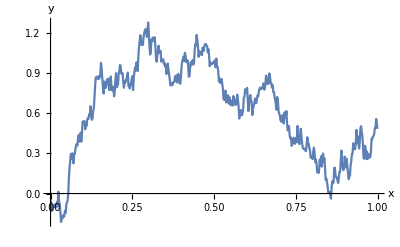
-Graphics-tW(t)

```mathematica
start = 0.0;
T = 1.0;
steps = 500;
dt = T / steps;
t = Range[start,T-dt,dt];

M = 1000;

dW = Sqrt[dt] * RandomReal[NormalDistribution[0,1],steps];
W = Accumulate[dW];

U = Exp[t+0.5*W]
UMean = Mean[U]

ts = TimeSeries[W,{t}];


Labeled[ListLinePlot[ts,AxesLabel->{"x","y"}],{"t","W(t)"},{Bottom,Left},RotateLabel->True]
```